```mathematica
Needs["VariationalMethods`"]
```

```mathematica
EulerEquations[(a/y[t])Sqrt[1-y'[t]^2]+ q/y[t],y[t],t]
```

-(a+q √(1-y'[t]^2)-y'[t]^2 (a+q √(1-y'[t]^2))-a y[t] y''[t])/(y[t]^2 (1-y'[t]^2)^(3/2))==0

```mathematica
DSolve[{-(a+q √(1-y'[t]^2)-y'[t]^2 (a+q √(1-y'[t]^2))-a y[t] y''[t])/(y[t]^2 (1-y'[t]^2)^(3/2))==0,y[0]==ys,y'[0]==0},y[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{y[t]→(-q ys+a √(t^2+(a^2 ys^2)/(a-q)^2)-q √(t^2+(a^2 ys^2)/(a-q)^2))/(a-q)},{y[t]→(-q ys-a √(t^2+(a^2 ys^2)/(a-q)^2)+q √(t^2+(a^2 ys^2)/(a-q)^2))/(a-q)},{y[t]→(q ys-a √(t^2+(a^2 ys^2)/(a+q)^2)-q √(t^2+(a^2 ys^2)/(a+q)^2))/(a+q)},{y[t]→(q ys+a √(t^2+(a^2 ys^2)/(a+q)^2)+q √(t^2+(a^2 ys^2)/(a+q)^2))/(a+q)}}

```mathematica
(* Solution number 1 *)
```

```mathematica
D[(-q ys+a √(t^2+(a^2 ys^2)/(a-q)^2)-q √(t^2+(a^2 ys^2)/(a-q)^2))/(a-q),t]//FullSimplify
```

t/(√(t^2+(a^2 ys^2)/(a-q)^2))

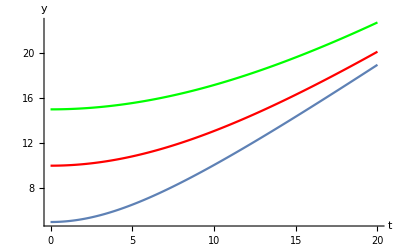

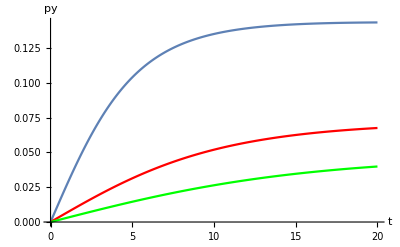

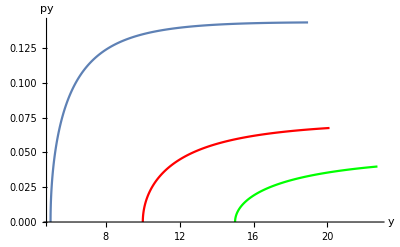

```mathematica
Block[
{y2,dy,py},
y2[t_,a_,ys_,q_]:=(-q ys+a √(t^2+(a^2 ys^2)/(a-q)^2)-q √(t^2+(a^2 ys^2)/(a-q)^2))/(a-q);
dy[t_,a_,ys_,q_]:=t/(√(t^2+(a^2 ys^2)/(a-q)^2));
py[t1_,a_,ys_,q_]:=a/y2[t1,a,ys,q]*dy[t1,a,ys,q]/Sqrt[1-dy[t1,a,ys,q]^2];
Print[
Show[
ListLinePlot[Table[{i,y2[i,1,05,0.32]},{i,0,20,0.05}],AxesLabel->{t,y}],
ListLinePlot[Table[{i,y2[i,1,10,0.32]},{i,0,20,0.05}],AxesLabel->{t,y},PlotStyle->Red],
ListLinePlot[Table[{i,y2[i,1,15,0.32]},{i,0,20,0.05}],AxesLabel->{t,y},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{i,py[i,1,05,0.32]},{i,0,20,0.05}],AxesLabel->{t,py}],
ListLinePlot[Table[{i,py[i,1,10,0.32]},{i,0,20,0.05}],AxesLabel->{t,py},PlotStyle->Red],
ListLinePlot[Table[{i,py[i,1,15,0.32]},{i,0,20,0.05}],AxesLabel->{t,py},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{y2[i,1,05,0.32],py[i,1,05,0.32]},{i,0,20,0.05}],AxesLabel->{y,py}],
ListLinePlot[Table[{y2[i,1,10,0.32],py[i,1,10,0.32]},{i,0,20,0.05}],AxesLabel->{y,py},PlotStyle->Red],
ListLinePlot[Table[{y2[i,1,15,0.32],py[i,1,15,0.32]},{i,0,20,0.05}],AxesLabel->{y,py},PlotStyle->Green],
PlotRange->All
]
];
]
```

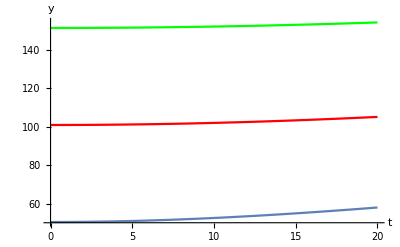

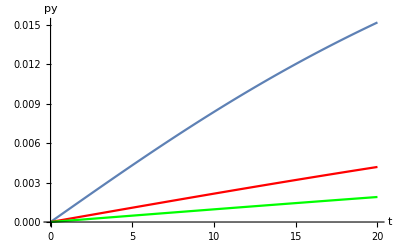

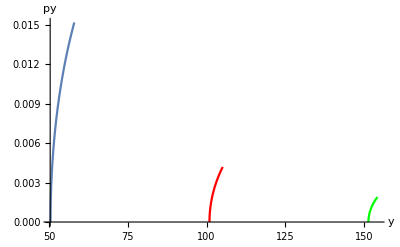

```mathematica
Block[
{y2,dy,py},
y2[t_,a_,ys_,q_]:=(-q ys+a √(t^2+(a^2 ys^2)/(a-q)^2)-q √(t^2+(a^2 ys^2)/(a-q)^2))/(a-q);
dy[t_,a_,ys_,q_]:=t/(√(t^2+(a^2 ys^2)/(a-q)^2));
py[t1_,a_,ys_,q_]:=a/y2[t1,a,ys,q]*dy[t1,a,ys,q]/Sqrt[1-dy[t1,a,ys,q]^2];
Print[
Show[
ListLinePlot[Table[{i,y2[i,1,05,1.22]},{i,0,20,0.05}],AxesLabel->{t,y}],
ListLinePlot[Table[{i,y2[i,1,10,1.22]},{i,0,20,0.05}],AxesLabel->{t,y},PlotStyle->Red],
ListLinePlot[Table[{i,y2[i,1,15,1.22]},{i,0,20,0.05}],AxesLabel->{t,y},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{i,py[i,1,05,1.22]},{i,0,20,0.05}],AxesLabel->{t,py}],
ListLinePlot[Table[{i,py[i,1,10,1.22]},{i,0,20,0.05}],AxesLabel->{t,py},PlotStyle->Red],
ListLinePlot[Table[{i,py[i,1,15,1.22]},{i,0,20,0.05}],AxesLabel->{t,py},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{y2[i,1,05,1.22],py[i,1,05,1.22]},{i,0,20,0.05}],AxesLabel->{y,py}],
ListLinePlot[Table[{y2[i,1,10,1.22],py[i,1,10,1.22]},{i,0,20,0.05}],AxesLabel->{y,py},PlotStyle->Red],
ListLinePlot[Table[{y2[i,1,15,1.22],py[i,1,15,1.22]},{i,0,20,0.05}],AxesLabel->{y,py},PlotStyle->Green],
PlotRange->All
]
];
]
```

```mathematica
(* Solution number 2 *)
```

```mathematica
D[(-q ys-a √(t^2+(a^2 ys^2)/(a-q)^2)+q √(t^2+(a^2 ys^2)/(a-q)^2))/(a-q),t]//FullSimplify
```

-t/(√(t^2+(a^2 ys^2)/(a-q)^2))

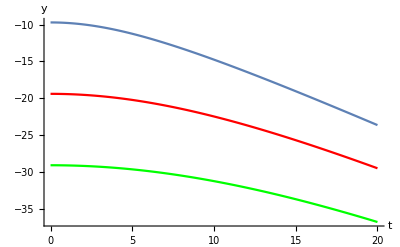

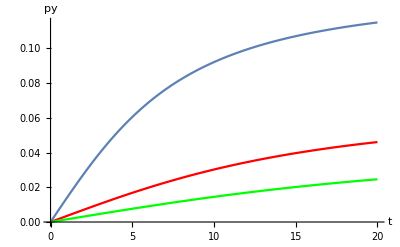

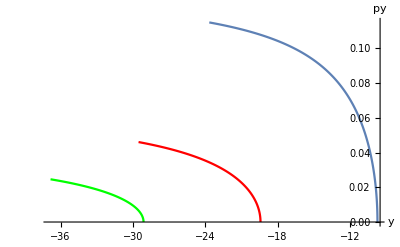

```mathematica
Block[
{y2,dy,py},
y2[t_,a_,ys_,q_]:=(-q ys-a √(t^2+(a^2 ys^2)/(a-q)^2)+q √(t^2+(a^2 ys^2)/(a-q)^2))/(a-q);
dy[t_,a_,ys_,q_]:=-t/(√(t^2+(a^2 ys^2)/(a-q)^2));
py[t1_,a_,ys_,q_]:=a/y2[t1,a,ys,q]*dy[t1,a,ys,q]/Sqrt[1-dy[t1,a,ys,q]^2];
Print[
Show[
ListLinePlot[Table[{i,y2[i,1,05,0.32]},{i,0,20,0.05}],AxesLabel->{t,y}],
ListLinePlot[Table[{i,y2[i,1,10,0.32]},{i,0,20,0.05}],AxesLabel->{t,y},PlotStyle->Red],
ListLinePlot[Table[{i,y2[i,1,15,0.32]},{i,0,20,0.05}],AxesLabel->{t,y},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{i,py[i,1,05,0.32]},{i,0,20,0.05}],AxesLabel->{t,py}],
ListLinePlot[Table[{i,py[i,1,10,0.32]},{i,0,20,0.05}],AxesLabel->{t,py},PlotStyle->Red],
ListLinePlot[Table[{i,py[i,1,15,0.32]},{i,0,20,0.05}],AxesLabel->{t,py},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{y2[i,1,05,0.32],py[i,1,05,0.32]},{i,0,20,0.05}],AxesLabel->{y,py}],
ListLinePlot[Table[{y2[i,1,10,0.32],py[i,1,10,0.32]},{i,0,20,0.05}],AxesLabel->{y,py},PlotStyle->Red],
ListLinePlot[Table[{y2[i,1,15,0.32],py[i,1,15,0.32]},{i,0,20,0.05}],AxesLabel->{y,py},PlotStyle->Green],
PlotRange->All
]
];
]
```

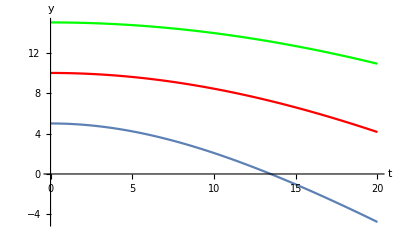

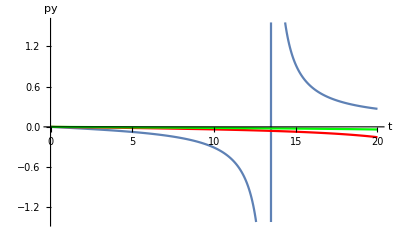

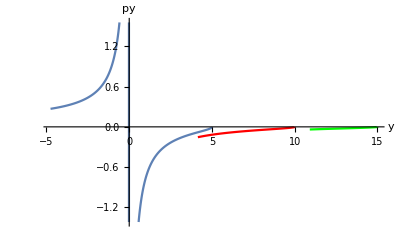

```mathematica
Block[
{y2,dy,py},
y2[t_,a_,ys_,q_]:=(-q ys-a √(t^2+(a^2 ys^2)/(a-q)^2)+q √(t^2+(a^2 ys^2)/(a-q)^2))/(a-q);
dy[t_,a_,ys_,q_]:=-t/(√(t^2+(a^2 ys^2)/(a-q)^2));
py[t1_,a_,ys_,q_]:=a/y2[t1,a,ys,q]*dy[t1,a,ys,q]/Sqrt[1-dy[t1,a,ys,q]^2];
Print[
Show[
ListLinePlot[Table[{i,y2[i,1,05,1.32]},{i,0,20,0.05}],AxesLabel->{t,y}],
ListLinePlot[Table[{i,y2[i,1,10,1.32]},{i,0,20,0.05}],AxesLabel->{t,y},PlotStyle->Red],
ListLinePlot[Table[{i,y2[i,1,15,1.32]},{i,0,20,0.05}],AxesLabel->{t,y},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{i,py[i,1,05,1.32]},{i,0,20,0.05}],AxesLabel->{t,py}],
ListLinePlot[Table[{i,py[i,1,10,1.32]},{i,0,20,0.05}],AxesLabel->{t,py},PlotStyle->Red],
ListLinePlot[Table[{i,py[i,1,15,1.32]},{i,0,20,0.05}],AxesLabel->{t,py},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{y2[i,1,05,1.32],py[i,1,05,1.32]},{i,0,20,0.05}],AxesLabel->{y,py}],
ListLinePlot[Table[{y2[i,1,10,1.32],py[i,1,10,1.32]},{i,0,20,0.05}],AxesLabel->{y,py},PlotStyle->Red],
ListLinePlot[Table[{y2[i,1,15,1.32],py[i,1,15,1.32]},{i,0,20,0.05}],AxesLabel->{y,py},PlotStyle->Green],
PlotRange->All
]
];
]
```

```mathematica
(* Solution number 3 *)
```

```mathematica
D[(q ys-a √(t^2+(a^2 ys^2)/(a+q)^2)-q √(t^2+(a^2 ys^2)/(a+q)^2))/(a+q),t]//FullSimplify
```

-t/(√(t^2+(a^2 ys^2)/(a+q)^2))

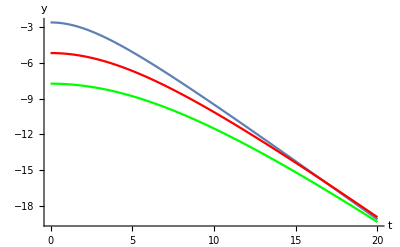

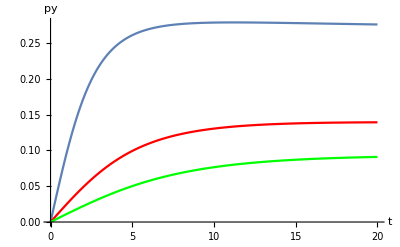

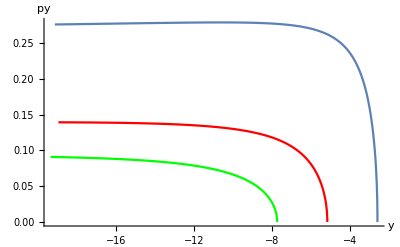

```mathematica
Block[
{y2,dy,py},
y2[t_,a_,ys_,q_]:=(q ys-a √(t^2+(a^2 ys^2)/(a+q)^2)-q √(t^2+(a^2 ys^2)/(a+q)^2))/(a+q);
dy[t_,a_,ys_,q_]:=-t/(√(t^2+(a^2 ys^2)/(a+q)^2));
py[t1_,a_,ys_,q_]:=a/y2[t1,a,ys,q]*dy[t1,a,ys,q]/Sqrt[1-dy[t1,a,ys,q]^2];
Print[
Show[
ListLinePlot[Table[{i,y2[i,1,05,0.32]},{i,0,20,0.05}],AxesLabel->{t,y}],
ListLinePlot[Table[{i,y2[i,1,10,0.32]},{i,0,20,0.05}],AxesLabel->{t,y},PlotStyle->Red],
ListLinePlot[Table[{i,y2[i,1,15,0.32]},{i,0,20,0.05}],AxesLabel->{t,y},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{i,py[i,1,05,0.32]},{i,0,20,0.05}],AxesLabel->{t,py}],
ListLinePlot[Table[{i,py[i,1,10,0.32]},{i,0,20,0.05}],AxesLabel->{t,py},PlotStyle->Red],
ListLinePlot[Table[{i,py[i,1,15,0.32]},{i,0,20,0.05}],AxesLabel->{t,py},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{y2[i,1,05,0.32],py[i,1,05,0.32]},{i,0,20,0.05}],AxesLabel->{y,py}],
ListLinePlot[Table[{y2[i,1,10,0.32],py[i,1,10,0.32]},{i,0,20,0.05}],AxesLabel->{y,py},PlotStyle->Red],
ListLinePlot[Table[{y2[i,1,15,0.32],py[i,1,15,0.32]},{i,0,20,0.05}],AxesLabel->{y,py},PlotStyle->Green],
PlotRange->All
]
];
]
```

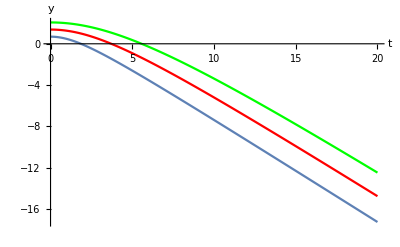

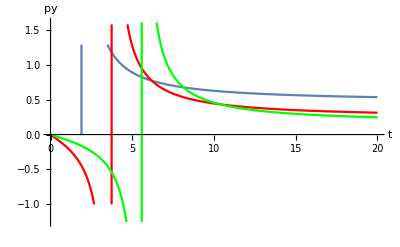

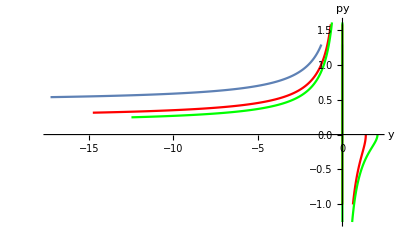

```mathematica
Block[
{y2,dy,py},
y2[t_,a_,ys_,q_]:=(q ys-a √(t^2+(a^2 ys^2)/(a+q)^2)-q √(t^2+(a^2 ys^2)/(a+q)^2))/(a+q);
dy[t_,a_,ys_,q_]:=-t/(√(t^2+(a^2 ys^2)/(a+q)^2));
py[t1_,a_,ys_,q_]:=a/y2[t1,a,ys,q]*dy[t1,a,ys,q]/Sqrt[1-dy[t1,a,ys,q]^2];
Print[
Show[
ListLinePlot[Table[{i,y2[i,1,05,1.32]},{i,0,20,0.05}],AxesLabel->{t,y}],
ListLinePlot[Table[{i,y2[i,1,10,1.32]},{i,0,20,0.05}],AxesLabel->{t,y},PlotStyle->Red],
ListLinePlot[Table[{i,y2[i,1,15,1.32]},{i,0,20,0.05}],AxesLabel->{t,y},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{i,py[i,1,05,1.32]},{i,0,20,0.05}],AxesLabel->{t,py}],
ListLinePlot[Table[{i,py[i,1,10,1.32]},{i,0,20,0.05}],AxesLabel->{t,py},PlotStyle->Red],
ListLinePlot[Table[{i,py[i,1,15,1.32]},{i,0,20,0.05}],AxesLabel->{t,py},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{y2[i,1,05,1.32],py[i,1,05,1.32]},{i,0,20,0.05}],AxesLabel->{y,py}],
ListLinePlot[Table[{y2[i,1,10,1.32],py[i,1,10,1.32]},{i,0,20,0.05}],AxesLabel->{y,py},PlotStyle->Red],
ListLinePlot[Table[{y2[i,1,15,1.32],py[i,1,15,1.32]},{i,0,20,0.05}],AxesLabel->{y,py},PlotStyle->Green],
PlotRange->All
]
];
]
```

```mathematica
(* Solution number 4 *)
```

```mathematica
D[(q ys+a √(t^2+(a^2 ys^2)/(a+q)^2)+q √(t^2+(a^2 ys^2)/(a+q)^2))/(a+q),t]//FullSimplify
```

t/(√(t^2+(a^2 ys^2)/(a+q)^2))

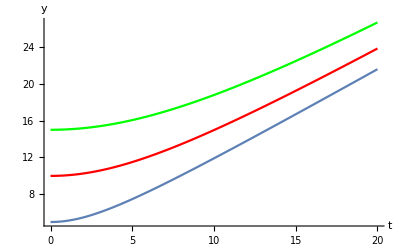

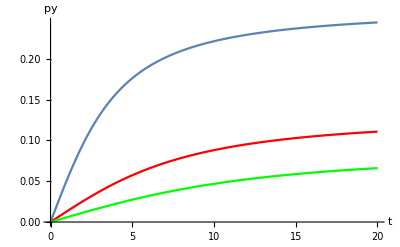

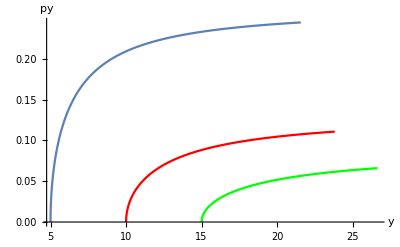

```mathematica
Block[
{y2,dy,py},
y2[t_,a_,ys_,q_]:=(q ys+a √(t^2+(a^2 ys^2)/(a+q)^2)+q √(t^2+(a^2 ys^2)/(a+q)^2))/(a+q);
dy[t_,a_,ys_,q_]:=t/(√(t^2+(a^2 ys^2)/(a+q)^2));
py[t1_,a_,ys_,q_]:=a/y2[t1,a,ys,q]*dy[t1,a,ys,q]/Sqrt[1-dy[t1,a,ys,q]^2];
Print[
Show[
ListLinePlot[Table[{i,y2[i,1,05,0.32]},{i,0,20,0.05}],AxesLabel->{t,y}],
ListLinePlot[Table[{i,y2[i,1,10,0.32]},{i,0,20,0.05}],AxesLabel->{t,y},PlotStyle->Red],
ListLinePlot[Table[{i,y2[i,1,15,0.32]},{i,0,20,0.05}],AxesLabel->{t,y},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{i,py[i,1,05,0.32]},{i,0,20,0.05}],AxesLabel->{t,py}],
ListLinePlot[Table[{i,py[i,1,10,0.32]},{i,0,20,0.05}],AxesLabel->{t,py},PlotStyle->Red],
ListLinePlot[Table[{i,py[i,1,15,0.32]},{i,0,20,0.05}],AxesLabel->{t,py},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{y2[i,1,05,0.32],py[i,1,05,0.32]},{i,0,20,0.05}],AxesLabel->{y,py}],
ListLinePlot[Table[{y2[i,1,10,0.32],py[i,1,10,0.32]},{i,0,20,0.05}],AxesLabel->{y,py},PlotStyle->Red],
ListLinePlot[Table[{y2[i,1,15,0.32],py[i,1,15,0.32]},{i,0,20,0.05}],AxesLabel->{y,py},PlotStyle->Green],
PlotRange->All
]
];
]
```

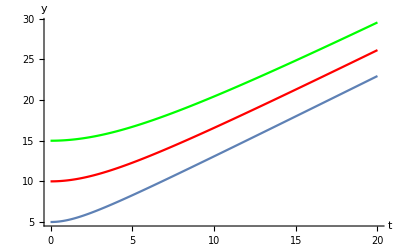

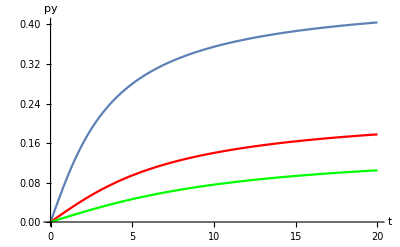

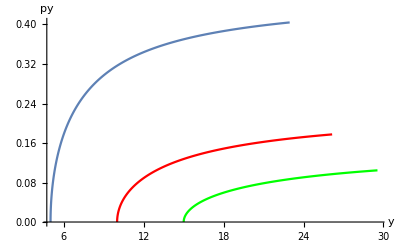

```mathematica
Block[
{y2,dy,py},
y2[t_,a_,ys_,q_]:=(q ys+a √(t^2+(a^2 ys^2)/(a+q)^2)+q √(t^2+(a^2 ys^2)/(a+q)^2))/(a+q);
dy[t_,a_,ys_,q_]:=t/(√(t^2+(a^2 ys^2)/(a+q)^2));
py[t1_,a_,ys_,q_]:=a/y2[t1,a,ys,q]*dy[t1,a,ys,q]/Sqrt[1-dy[t1,a,ys,q]^2];
Print[
Show[
ListLinePlot[Table[{i,y2[i,1,05,1.32]},{i,0,20,0.05}],AxesLabel->{t,y}],
ListLinePlot[Table[{i,y2[i,1,10,1.32]},{i,0,20,0.05}],AxesLabel->{t,y},PlotStyle->Red],
ListLinePlot[Table[{i,y2[i,1,15,1.32]},{i,0,20,0.05}],AxesLabel->{t,y},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{i,py[i,1,05,1.32]},{i,0,20,0.05}],AxesLabel->{t,py}],
ListLinePlot[Table[{i,py[i,1,10,1.32]},{i,0,20,0.05}],AxesLabel->{t,py},PlotStyle->Red],
ListLinePlot[Table[{i,py[i,1,15,1.32]},{i,0,20,0.05}],AxesLabel->{t,py},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{y2[i,1,05,1.32],py[i,1,05,1.32]},{i,0,20,0.05}],AxesLabel->{y,py}],
ListLinePlot[Table[{y2[i,1,10,1.32],py[i,1,10,1.32]},{i,0,20,0.05}],AxesLabel->{y,py},PlotStyle->Red],
ListLinePlot[Table[{y2[i,1,15,1.32],py[i,1,15,1.32]},{i,0,20,0.05}],AxesLabel->{y,py},PlotStyle->Green],
PlotRange->All
]
];
]
```